```mathematica
Some basic information;
```

```mathematica
alatts={4.575,4.600,4.625,4.6583,4.685,4.730,4.759,4.801,4.850};
tempps={0,10,300,500,760,1000,1500,1900,2500,3200,3800};
temppps=tempps[[2;;11]];
temps2={300,300,760,1900,2500,3200,3800};
temps3={300,760,1900,2500,3200,3800};
THz2meV=1/4.135665538536;K2meV=0.086173324;kjmol2evatom=1/(96.487*64);
Nat=64;Natvac=63;mass={91.224,12.0107,1};
ang2bohr=1/0.529177208;ev2har=1/27.211396;kB=1000*8.617332478*10^−5;
eVperAng2harperbohr=ev2har/ang2bohr;eVperAng22harperbohr2=ev2har/ang2bohr/ang2bohr;
HarBohr=meVperAng22harperbohr2=0.001*ev2har/ang2bohr/ang2bohr;
(*Constant, Fermi-Dirac and Fermi-Dirac changing with energy*)
K2eV=8.617332478*10^−5;
fermiDirac[energy_,temp_]:=1/(Exp[energy/(K2eV*temp)]+1)
(*define sigma and8 kappa kernels*)
(*temp in energy units*)
sigmaK[energy_,temp_]:=-D[fermiDirac[energy,temp],energy]
kappaK[energy_,temp_]:=-(1/temp)*(energy^2)*D[fermiDirac[energy,temp],energy]
eV2ryd=1/13.605698066;ryd2eV=13.605698066;
```

```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/NEB/FINAL_PATHS_FOR_PAPER/"];
file={"7_vol_temp_dist_energy"};
NEBdata=Table[ReadList[file[[i]],{Number, Number,Number, Number,Number, Number,Number, Number,Number, Number,Number, Number,Number}],{i,1,1}][[1]];
```

#### esscape distance

```mathematica
0.07924*4.6583*2
0.07924*4.759*2
0.07924*4.850*2
```

0.738247

0.754206

0.768628

```mathematica
index=Transpose[NEBdata][[{1}]][[1]]
vols=Transpose[NEBdata][[{2,6,10}]]
temp=Transpose[NEBdata][[{3,7,11}]]
dist=Transpose[NEBdata][[{4,8,12}]]
e0s=Transpose[NEBdata][[{5,9,13}]]
```

{1,2,3,4,5,6,7}

{{4.6583,4.6583,4.6583,4.6583,4.6583,4.6583,4.6583},{4.759,4.759,4.759,4.759,4.759,4.759,4.759},{4.85,4.85,4.85,4.85,4.85,4.85,4.85}}

{{0,0,0,0,0,0,0},{2479,2479,2479,2479,2479,2479,2479},{3821,3821,3821,3821,3821,3821,3821}}

{{-1.36791,0.,1.36791,2.41825,2.75902,3.2993,4.77579},{-1.28672,0.,1.28672,2.65931,3.07087,3.5768,5.08521},{-1.24095,0.,1.24096,2.69568,3.17703,3.66887,5.20612}}

{{4.572,0.,4.572,3.967,4.036,3.577,5.743},{4.00966,0.,4.00966,3.12443,3.24303,2.82737,4.905},{3.47984,0.,3.47984,2.30252,2.48612,2.07754,4.067}}

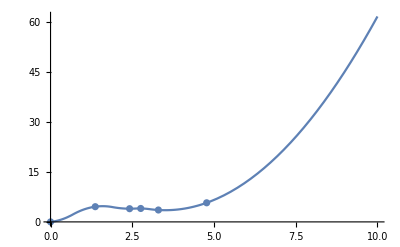

```mathematica
diste0s=Table[Transpose@{dist[[i]],e0s[[i]]},{i,1,3}];
ListLinePlot@diste0s;
Show[{Plot[Interpolation[diste0s[[1]],Method->"Spline",InterpolationOrder->2][x],{x,0,10}],ListPlot@diste0s[[1]]}]
```

```mathematica
(*Function to force the gradients to be correct either side*)
deltaX=0.5;
deltaForce=0.00005
F[{a_,b_},j_]:={{a,b},{a+deltaX/1000,b+((-1)^(j))deltaForce},{a-deltaX/1000,b+((-1)^(j))deltaForce}}
diste0sGrad=Table[Partition[Flatten@Table[F[diste0s[[i]][[j]],j],{j,1,Length[diste0s[[i]]]}],2],{i,1,3}]
diste0sGradGP=Table[Flatten[{#1->#2}&@@@diste0sGrad[[i]]],{i,1,3}]
Pdiste0sGradGP=Table[Predict[diste0sGradGP[[i]],Method->"GaussianProcess"],{i,1,3}]
```

0.00005

{{{-1.36791,4.572},{-1.36741,4.57195},{-1.36841,4.57195},{0.,0.},{0.0005,0.00005},{-0.0005,0.00005},{1.36791,4.572},{1.36841,4.57195},{1.36741,4.57195},{2.41825,3.967},{2.41875,3.96705},{2.41775,3.96705},{2.75902,4.036},{2.75952,4.03595},{2.75852,4.03595},{3.2993,3.577},{3.2998,3.57705},{3.2988,3.57705},{4.77579,5.743},{4.77629,5.74295},{4.77529,5.74295}},{{-1.28672,4.00966},{-1.28622,4.00961},{-1.28722,4.00961},{0.,0.},{0.0005,0.00005},{-0.0005,0.00005},{1.28672,4.00966},{1.28722,4.00961},{1.28622,4.00961},{2.65931,3.12443},{2.65981,3.12448},{2.65881,3.12448},{3.07087,3.24303},{3.07137,3.24298},{3.07037,3.24298},{3.5768,2.82737},{3.5773,2.82742},{3.5763,2.82742},{5.08521,4.905},{5.08571,4.90495},{5.08471,4.90495}},{{-1.24095,3.47984},{-1.24045,3.47979},{-1.24145,3.47979},{0.,0.},{0.0005,0.00005},{-0.0005,0.00005},{1.24096,3.47984},{1.24146,3.47979},{1.24046,3.47979},{2.69568,2.30252},{2.69618,2.30257},{2.69518,2.30257},{3.17703,2.48612},{3.17753,2.48607},{3.17653,2.48607},{3.66887,2.07754},{3.66937,2.07759},{3.66837,2.07759},{5.20612,4.067},{5.20662,4.06695},{5.20562,4.06695}}}

{{-1.36791→4.572,-1.36741→4.57195,-1.36841→4.57195,0.→0.,0.0005→0.00005,-0.0005→0.00005,1.36791→4.572,1.36841→4.57195,1.36741→4.57195,2.41825→3.967,2.41875→3.96705,2.41775→3.96705,2.75902→4.036,2.75952→4.03595,2.75852→4.03595,3.2993→3.577,3.2998→3.57705,3.2988→3.57705,4.77579→5.743,4.77629→5.74295,4.77529→5.74295},{-1.28672→4.00966,-1.28622→4.00961,-1.28722→4.00961,0.→0.,0.0005→0.00005,-0.0005→0.00005,1.28672→4.00966,1.28722→4.00961,1.28622→4.00961,2.65931→3.12443,2.65981→3.12448,2.65881→3.12448,3.07087→3.24303,3.07137→3.24298,3.07037→3.24298,3.5768→2.82737,3.5773→2.82742,3.5763→2.82742,5.08521→4.905,5.08571→4.90495,5.08471→4.90495},{-1.24095→3.47984,-1.24045→3.47979,-1.24145→3.47979,0.→0.,0.0005→0.00005,-0.0005→0.00005,1.24096→3.47984,1.24146→3.47979,1.24046→3.47979,2.69568→2.30252,2.69618→2.30257,2.69518→2.30257,3.17703→2.48612,3.17753→2.48607,3.17653→2.48607,3.66887→2.07754,3.66937→2.07759,3.66837→2.07759,5.20612→4.067,5.20662→4.06695,5.20562→4.06695}}

{PredictorFunction[…],PredictorFunction[…],PredictorFunction[…]}

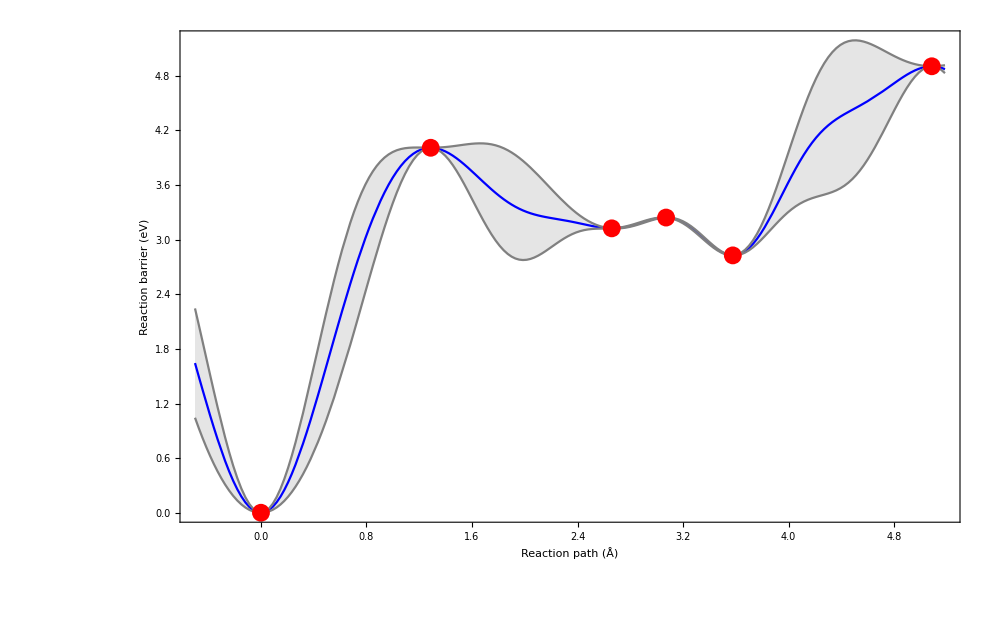

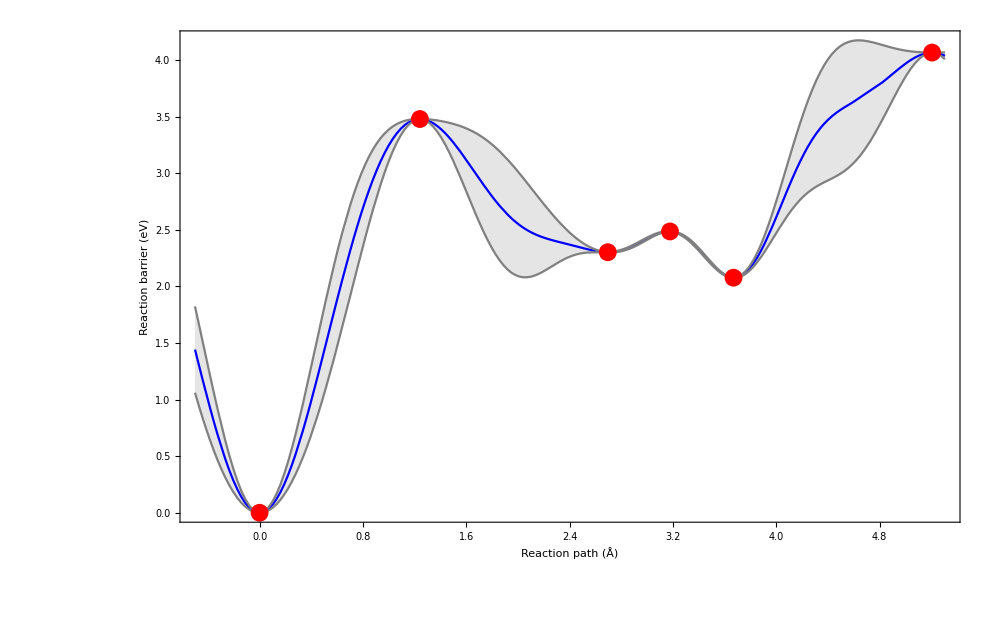

```mathematica
With[{vol=2},Show[Plot[{Pdiste0sGradGP[[vol]][x],Pdiste0sGradGP[[vol]][x]+StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]],Pdiste0sGradGP[[vol]][x]-StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]]},{x,-0.5,Evaluate[dist[[vol]][[-1]]]+0.1},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->"None",PerformanceGoal->"Speed",PlotLegends->Placed[{"Prediction","1-σ confidence interval"},{0.2,0.8}],Frame->True,FrameLabel->{Style["Reaction path (Å)",FontSize->12],Style["Reaction barrier (eV)",FontSize->12]},ImageSize->1000],ListPlot[diste0s[[vol]],PlotStyle->Red,PlotLegends->Placed[legends[[vol]],{0.2,0.8}]]]]
With[{vol=3},Show[Plot[{Pdiste0sGradGP[[vol]][x],Pdiste0sGradGP[[vol]][x]+StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]],Pdiste0sGradGP[[vol]][x]-StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]]},{x,-0.5,Evaluate[dist[[vol]][[-1]]]+0.1},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->"None",PerformanceGoal->"Speed",PlotLegends->Placed[{"Prediction","1-σ confidence interval"},{0.2,0.8}],Frame->True,FrameLabel->{Style["Reaction path (Å)",FontSize->12],Style["Reaction barrier (eV)",FontSize->12]},ImageSize->1000],ListPlot[diste0s[[vol]],PlotStyle->Red,PlotLegends->Placed[legends[[vol]],{0.2,0.8}]]]]
```

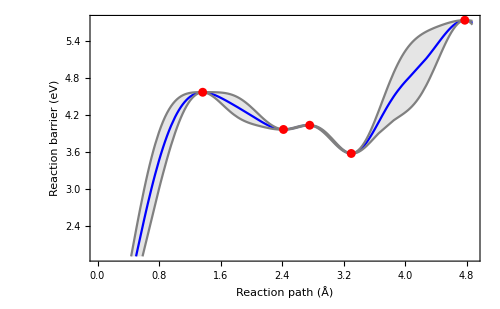

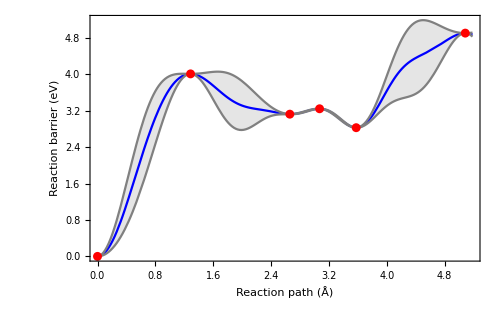

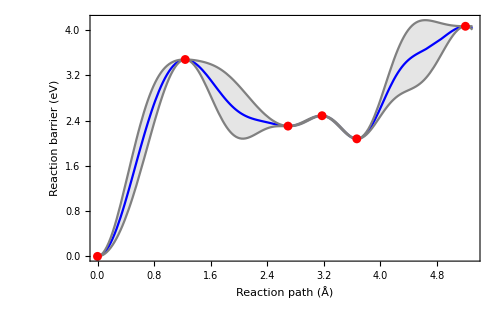

```mathematica
gp1=With[{vol=1},Show[Plot[{Pdiste0sGradGP[[vol]][x],Pdiste0sGradGP[[vol]][x]+StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]],Pdiste0sGradGP[[vol]][x]-StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]]},{x,0,Evaluate[dist[[vol]][[-1]]+0.1]},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->"None",PerformanceGoal->"Speed",PlotLegends->Placed[{"Prediction","1-σ confidence interval"},{0.2,0.8}],Frame->True,FrameLabel->{Style["Reaction path (Å)",FontSize->12],Style["Reaction barrier (eV)",FontSize->12]},ImageSize->500],ListPlot[List@@@diste0s[[vol]],PlotStyle->Red,PlotLegends->Placed[legends[[vol]],{0.2,0.8}]]]]
gp2=With[{vol=2},Show[Plot[{Pdiste0sGradGP[[vol]][x],Pdiste0sGradGP[[vol]][x]+StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]],Pdiste0sGradGP[[vol]][x]-StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]]},{x,0,Evaluate[dist[[vol]][[-1]]+0.1]},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->"None",PerformanceGoal->"Speed",PlotLegends->Placed[{"Prediction","1-σ confidence interval"},{0.2,0.8}],Frame->True,FrameLabel->{Style["Reaction path (Å)",FontSize->12],Style["Reaction barrier (eV)",FontSize->12]},ImageSize->500],ListPlot[diste0s[[vol]],PlotStyle->Red,PlotLegends->Placed[legends[[vol]],{0.2,0.8}]]]]
gp3=With[{vol=3},Show[Plot[{Pdiste0sGradGP[[vol]][x],Pdiste0sGradGP[[vol]][x]+StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]],Pdiste0sGradGP[[vol]][x]-StandardDeviation[Pdiste0sGradGP[[vol]][x,"Distribution"]]},{x,0,Evaluate[dist[[vol]][[-1]]+0.1]},PlotStyle->{Blue,Gray,Gray},Filling->{2->{3}},Exclusions->"None",PerformanceGoal->"Speed",PlotLegends->Placed[{"Prediction","1-σ confidence interval"},{0.2,0.8}],Frame->True,FrameLabel->{Style["Reaction path (Å)",FontSize->12],Style["Reaction barrier (eV)",FontSize->12]},ImageSize->500],ListPlot[diste0s[[vol]],PlotStyle->Red,PlotLegends->Placed[legends[[vol]],{0.2,0.8}]]]]
```

```mathematica
volshort=Table[vols[[i]][[1]],{i,1,3}]
list2=Partition[Flatten@Table[Join@Table[{volshort[[j]],i/10,Pdiste0sGradGP[[j]][i/10]},{i,-6,Floor[10*dist[[j]][[-1]]]}],{j,1,3}],3];
volDistE0GP={#1->#2&&#3}&@@@list2;
```

{4.6583,4.759,4.85}

```mathematica
ListPointPlot3D[list2,Filling->Bottom,FillingStyle->Directive[Thick],AxesLabel->{"Volume (Å^3)","Reaction Path (Å)","Reaction Barier \n(eV/defect)"}]
```

-Graphics3D-

```mathematica
Show[{ListPointPlot3D[list2,Filling->Bottom,FillingStyle->Directive[Thick],AxesLabel->{"Volume (Å^3)","Reaction Path (Å)","Energy \n(eV/defect)"},ImageSize->600],ListPlot3D[list2,Mesh->None,ColorFunction->"Rainbow",InterpolationOrder->3,PlotStyle->Opacity[0.15],BoundaryStyle->Directive[Black,Thick],Filling->Bottom,AxesLabel->{"Volume (Å^3)","Reaction Path (Å)","Energy \n(eV/defect)"}]}]
```

-Graphics3D-

```mathematica
Show[{ListPointPlot3D[list2,FillingStyle->Directive[Thick],AxesLabel->{"Volume (Å^3)","Reaction Path (Å)","Reaction Barier \n(eV/defect)"},ImageSize->600],ListPlot3D[list2,Mesh->None,InterpolationOrder->3,PlotStyle->Directive[Opacity[0.8],Orange,Specularity[White,50]],BoundaryStyle->Directive[Black,Thick],Filling->Bottom,AxesLabel->{"Volume (Å^3)","Reaction Path (Å)","Reaction Barier \n(eV/defect)"}]}]
```

-Graphics3D-

```mathematica
FrameLabel->{Style["Reaction path (Å)",FontSize->12],Style["Reaction barrier (eV)",FontSize->12]}
```

FrameLabel→{Reaction path (Å),Reaction barrier (eV)}

```mathematica
neb0=Show[{ListPlot3D[list2,Mesh->None,InterpolationOrder->3,Axes->True,TicksStyle->15,PlotLabel->Style["Frenkel recombination energy surface",15],Filling->Bottom,Boxed->False,PlotStyle->Opacity[0.75],BoundaryStyle->Directive[Black,Thick],AxesLabel->{Style["Volume (Å)",FontSize->15],Style["Reaction Path (Å)",FontSize->15],Style["Reaction Barier \n(eV/defect)",FontSize->15]},ImageSize->400],ListPointPlot3D[list2,Filling->Bottom,FillingStyle->Directive[Thick]]}]
```

-Graphics3D-

```mathematica
neb1=Show[{ListPlot3D[list2,Mesh->None,InterpolationOrder->3,Axes->True,PlotLabel->"",Filling->Bottom,Boxed->True,BoxStyle->Dashing[0.02],PlotStyle->Opacity[0.75],BoundaryStyle->Directive[Black,Thick],AxesStyle->Directive[Black,20,Thickness[0.008]],AxesLabel->{Style["a (Å)",FontSize->20,Black],Style["Path (Å)",FontSize->20,Black],Style["E \n(eV)",FontSize->20,Black]},ImageSize->700],ListPointPlot3D[list2,Filling->Bottom,FillingStyle->Directive[Thick]]},ViewPoint->{3.9,1.0,0.8},Ticks->{ {4.66,4.76,4.85}, {0,1,2,3,4,5},{0,1,2,3,4,5}}]
```

-Graphics3D-